```mathematica
ρ0=1;
L1=Lx;
L2=Ly;
γ=1.4;
c=1.4;
eps=0.000001;
alphaa=2;
timeP = 2.0;
initrho[r_]:=eps Exp[-alphaa r^2]
```

```mathematica
NIntegrate[initrho[x,y],{x,0,4},{y,0,4}]
```

NIntegrate::inumr: The integrand initrho[x,y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,4},{0,4}}.

NIntegrate[initrho[x,y],{x,0,4},{y,0,4}]

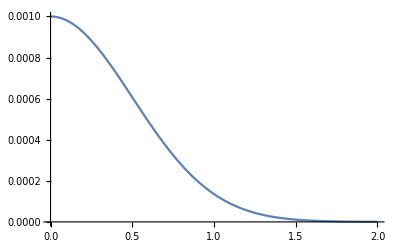

```mathematica
Plot[initrho[r],{r,0,2}]
```

### Analytical solutions for density, velocity, pressure, energy

```mathematica
rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=eps/(2alphaa)NIntegrate[Exp[-ξ^2/(4alphaa)]Cos[ξ t]BesselJ[0,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞},Method->{Automatic,"SymbolicProcessing"->False},MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15 ]
```

```mathematica
uAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(eps(x-L1/2))/(2alphaa √((x-L1/2)^2+(y-L2/2)^2))NIntegrate[Exp[-ξ^2/(4alphaa)]Sin[ξ t]BesselJ[1,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
vAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(eps(y-L2/2))/(2alphaa √((x-L1/2)^2+(y-L2/2)^2))NIntegrate[Exp[-ξ^2/(4alphaa)]Sin[ξ t]BesselJ[1,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
```

```mathematica
mcrCenterLine=MeshCellRcm[[nx ny/2+1;;nx ny/2+nx]];
```

```mathematica
mmm=Table[MeshCellRcm[[i]],{i,MeshCellRcm//Length}];
```

```mathematica
rhoAn[mmm[[1,1]],mmm[[1,2]],2.0]
```

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 2.05202×10^-10 and 1.4803×10^-7 for the integral and error estimates.

5.13005×10^-17

### Center values for graphics

```mathematica
dataAnCenterRhoEqP=ParallelTable[{mmm[[i,1]],rhoAn[mmm[[i,1]],mmm[[i,2]],timeP]+1},{i,mcrCenterLine//Length}];
dataAnCenterU=ParallelTable[{mmm[[i,1]],uAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
dataAnCenterV=ParallelTable[{mmm[[i,1]],vAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
```

```mathematica
dataAnCenterE=Transpose@{dataAnCenterRhoEqP[[All,1]],dataAnCenterRhoEqP[[All,2]]/(γ-1)+1/2 dataAnCenterRhoEqP[[All,2]](dataAnCenterU[[All,2]]*dataAnCenterU[[All,2]] + dataAnCenterV[[All,2]]*dataAnCenterV[[All,2]])};
```

```mathematica
dataAnCenterH=Transpose@{dataAnCenterRhoEqP[[All,1]],1/dataAnCenterRhoEqP[[All,2]](dataAnCenterE[[All,2]] + dataAnCenterRhoEqP[[All,2]])};
```

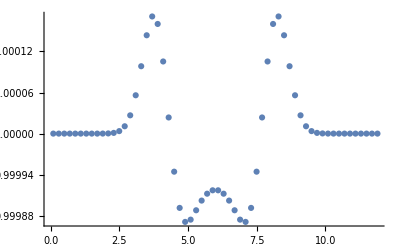

```mathematica
dataExact=ListPlot[dataAnCenterRhoEqP,PlotRange->All]
```

### Mean integral values for error analysis

```mathematica
area=hx hy
```

0.04

```mathematica
cellNodes=Table[{
{MeshCellRcm[[i,1]]-hx/2,MeshCellRcm[[i,2]]-hy/2},
{MeshCellRcm[[i,1]]+hx/2,MeshCellRcm[[i,2]]-hy/2},
{MeshCellRcm[[i,1]]+hx/2,MeshCellRcm[[i,2]]+hy/2},
{MeshCellRcm[[i,1]]-hx/2,MeshCellRcm[[i,2]]+hy/2}},
{i,MeshCellRcm//Length}];
```

```mathematica
cells=Table[Polygon[cellNodes[[i]]],{i,1,cellNodes//Length}];
cells[[1]]
```

Polygon[{{0.,0.},{0.2,0.},{0.2,0.2},{0.,0.2}}]

```mathematica
Clear[cellNodes]
```

```mathematica
fDiffer[x_,y_,t_,n_]:=Abs[rhoAn[x,y,t]-GetSol[alpha,n,1,{x,y}]+1]
```

#### NormC

```mathematica
NMaxValue[{fDiffer[x,y,timeP,1],{x,y}∈cells[[1]]},{x,y}]
```

5.41147×10^-11

```mathematica
maxitable=ParallelTable[NMaxValue[{fDiffer[x,y,timeP,n],{x,y}∈cells[[n]]},{x,y}],{n,1,nx ny}];
maxitable[[1]]
```

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
                                              -8
    . NIntegrate obtained -2.74349674471548 10   and 0.0000901081934697336
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.0000717525846401650 and 0.0000624396040848532
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.00835717959723217 and 0.0000262969113377231
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.000458850345839826 and 0.0000355270511651730
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {5.41020160502635}
                                              -8
    . NIntegrate obtained -2.06787715129609 10   and 0.0000436953192944503
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.000143668044336128 and 0.0000700839531440049
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {5.41020160502635}
    . NIntegrate obtained 0.000848718442003782 and 0.0000156106078243482
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {5.41020160502635}
                                              -8
    . NIntegrate obtained -1.43161607641304 10   and 0.0000867886670658141
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.000190057453430166 and 0.0000663057857377041
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.0174492150325726 and 0.0000145453396042231
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {5.41020160502635}
    . NIntegrate obtained 0.000998931288978296 and 0.0000160006000298072
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.0199756712498679 and 0.0000291787046985917
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
                                             -8
    . NIntegrate obtained 7.74684320193161 10   and 0.000137662249741454
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
                                             -7
    . NIntegrate obtained 1.52537765309713 10   and 0.000128871046880980
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
                                             -7
    . NIntegrate obtained 2.10680069541156 10   and 0.000117304990163191
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.0318901928284402 and 0.0000303777867125309
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.0463472331790530 and 0.0000291760911359321
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.0541793803568189 and 0.0000260657731298859
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.494068323105642 and 0.0000103538557321434
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.496302243786277 and 0.0000103775512353374
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.537501352303751 and 0.0000103601176001600
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.0687787647691239 and 0.0000188696994332880
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.0588640727477275 and 0.0000238857806244153
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {7.01594636248225}
    . NIntegrate obtained 0.0749817739829506 and 0.0000156657521721847
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {5.41020160502635}
    . NIntegrate obtained 0.0000231651014883398 and 0.0000701407320465601
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {5.41020160502635}
    . NIntegrate obtained 0.0000328228439614845 and 0.0000342834632419381
     for the integral and error estimates.

NIntegrate::ncvb: 
   NIntegrate failed to converge to prescribed accuracy after 5
     recursive bisections in Î.be near {Î.be} = {5.41020160502635}
    . NIntegrate obtained 0.0000405009351380342 and 0.0000404274478518295
     for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb
     will be suppressed during this calculation.

$Aborted

4.27709×10^-9

```mathematica
Max[maxitable]
```

```mathematica
8.112305699191237*^-8
```

```mathematica
8.112305487071103*^-8
```

```mathematica
4.5730865555452755*^-8
```

```mathematica
5.6039898640702734*^-8
```

```mathematica
1.4663909406483854*^-7
```

```mathematica
3.49980129889861*^-8
```

#### Norm L1

```mathematica
NIntegrate[fDiffer[x,y,timeP,1],{x,y}∈cells[[1]],MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15]
```

```mathematica
intable=ParallelTable[NIntegrate[fDiffer[x,y,timeP,n],{x,y}∈cells[[n]],MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15],{n,1,nx ny}];
intable[[1]]
```

```mathematica
Sum[intable[[i]],{i,intable//Length}]
```

```mathematica
4.2946188445809258019148826416134`15.*^-7
```

```mathematica
1.39303387530596154344121589865928`15.*^-6
```

```mathematica
1.39680162709597125420651450137597`15.*^-6
```

```mathematica
1.39816238190462637371729712980992`5.*^-6
```

```mathematica
4.4620311025502396 ^-7
```

#### Norm L2

```mathematica
(*надо переделать - квадрат возмущения считают по всей расчетной области*)
```

```mathematica
insqrtable=ParallelTable[NIntegrate[fDiffer[x,y,timeP,n]^2,{x,y}∈cells[[n]],MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15],{n,1,nx ny}];
insqrtable[[1]]
```

9.42039396441656×10^-24

```mathematica
√Sum[insqrtable[[i]],{i,insqrtable//Length}]
```

```mathematica
8.097684201245305212998232964007`15.301029995663962*^-8
```

```mathematica
2.4485155921685051401437828656416`15.301029995663969*^-7
```

```mathematica
8.295058830784622 ^-8
```